Supplementary code for: Bert Wuyts, Jan Sieber, “Automated derivation of moment closures for multistate dynamics on networks” [in review with PRE]. https://arxiv.org/abs/2111.07643

# Moment equations for SIS spreading (4th order)

Bert Wuyts

Centre for Systems, Dynamics and Control, University of Exeter, United Kingdom

email: b3rtwu@gmail.com

In this notebook, we obtain the moment equations of SIS epidemic spreading (without making assumptions about the network type). This is a demo of our package for moment closure for dynamics on networks.

Load package

```mathematica
<<mfmcl`
```

Define the dynamical process

Example process: SIS spreading. Each process is defined by its state space on nodes (l)  and its conversion rates (R0: spontaneous, R1: nearest-neighbour induced). R0[[i,j]] is the rate at which l[[i]] spontaneously converts to l[[j]]. R1[[i,j,k]] is the rate at which l[[i]]  converts to l[[j]] for each link to l[[k]].

```mathematica
l={{"S",RGBColor[0.32, 0.65, 1]},{"I",RGBColor[1, 0.56, 0.11]}};n=Length[l]; (*state labels*)
R0={{0,0},{γ,0}}; (*I->S at rate γ*)
R1=ConstantArray[0,{n,n,n}]; 
R1[[All,All,2]]={{0,β},{0,0}};(*I<->S->I<->I at rate β*)
sisprocess={l,R0,R1};
```

Obtain moment equations

Here, we show how one can obtain the unclosed (and non-normalised) moment equations without consideration of the particular network, i.e. taking account of all possible motifs.

Choose truncation order (= max subgraph size):

```mathematica
k=4;
```

Find all possible induced subgraphs:






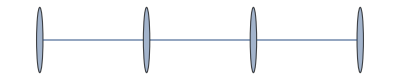
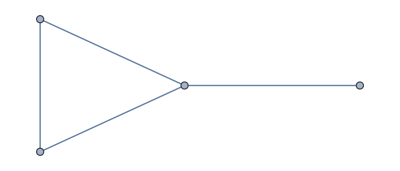
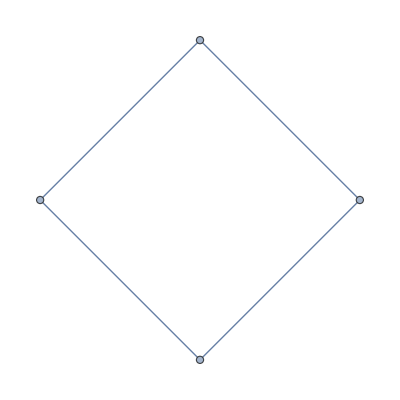
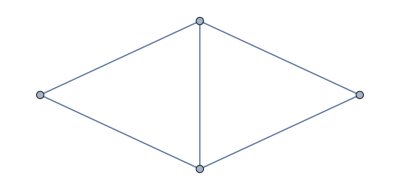
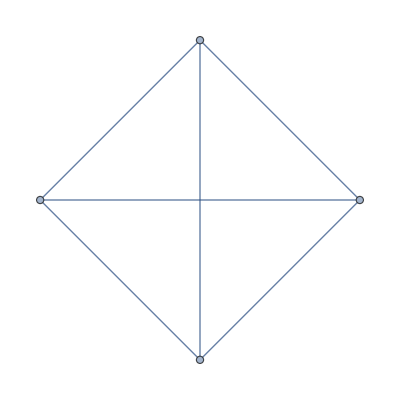

```mathematica
gs=enumerateGraphs/@Range[k]
```

Find all possible motifs (labelled subgraphs)

```mathematica
mots=Map[enumerateMotifs[#,l]&,gs,{2}]
```

{{{-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

Obtain moment equations

```mathematica
{Q,x,xkp1}=getMomentEqs[Flatten@gs,Flatten@mots,sisprocess,OutputFormat->"Matrix"];
```

```mathematica
x1kp1=x~Join~xkp1;
coeffTab[Q,x1kp1,True]
```

⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩ | ⟨-Graphics-⟩
. | γ | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | -γ | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | 2 γ | . | . | . | -2 β | . | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | -β-γ | γ | . | . | β | . | -β | . | . | β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | 2 β | -2 γ | . | . | . | . | 2 β | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | γ | 2 γ | . | . | . | . | . | . | . | . | . | -β | . | . | . | . | . | . | . | . | -2 β | . | . | . | . | . | . | . | . | -4 β | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | . | . | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | -2 β-γ | . | 2 γ | . | . | . | . | . | . | . | . | β | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | . | . | . | 2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | -β-γ | γ | γ | . | . | . | . | . | . | . | . | . | -β | . | . | . | . | . | . | β | . | . | . | -β | . | . | . | . | β | . | -β | . | . | . | -2 β | . | . | . | . | β | -β | . | . | . | . | β | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | β | β | -β-2 γ | . | γ | . | . | . | . | . | . | . | . | β | . | . | . | . | . | . | . | . | β | . | . | -β | . | . | . | . | β | β | . | . | . | β | -β | . | . | . | . | . | β | -β | . | . | . | β | . | β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | -2 β-2 γ | γ | . | . | . | . | . | . | . | . | . | . | -β | . | . | . | . | . | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | 2 β | . | -2 β | . | . | . | 2 β | . | . | . | . | . | . | . | 2 β | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | 2 β | 2 β | -3 γ | . | . | . | . | . | . | . | . | . | . | β | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | . | . | . | . | . | 2 β | . | . | . | . | . | . | 2 β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | 3 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -6 β | . | . | . | . | . | . | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | -2 β-γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | -2 β | . | -2 β | . | . | . | β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | 2 β | -2 β-2 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | -β | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | -2 β | . | . | . | 2 β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | 6 β | -3 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 6 β | . | . | . | . | 3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | γ | 3 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β | -β | -6 β | -6 β | -3 β | -9 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-γ | . | 3 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | 3 β | . | 3 β | β | -3 β | -6 β | -3 β | -3 β | -6 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β-γ | γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | 2 β | β | β | 2 β | β | . | . | . | . | . | . | -2 β | -β | -2 β | -2 β | -4 β | -β | -2 β | -3 β | -4 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | -2 β-2 γ | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | 2 β | β | β | 2 β | β | . | β | . | . | 2 β | β | . | β | 2 β | β | -2 β | -2 β | -2 β | -2 β | -2 β | -2 β | -2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β-2 γ | γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | 2 β | 2 β | . | 2 β | 2 β | 2 β | 2 β | . | . | . | . | . | . | . | . | -β | -β | -2 β | -2 β | -2 β | -β | -4 β | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | -β-3 γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | . | β | . | β | 2 β | . | 2 β | β | β | -β | -2 β | -β | -β | -2 β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | . | 6 β | 3 β | . | 3 β | 6 β | . | 3 β | . | . | . | . | . | . | -β | -3 β | -3 β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | 3 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | 6 β | 3 β | 3 β | 6 β | 3 β | β | 3 β | 3 β | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 γ | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | -2 β | -2 β | -4 β | -4 β | -2 β | -6 β | -6 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β-γ | γ | . | γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | β | β | β | 2 β | β | -β | -β | -β | -2 β | -2 β | -β | -2 β | -β | -β | -3 β | -2 β | -2 β | -2 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | -2 β-2 γ | . | . | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | 2 β | . | 2 β | 2 β | . | 2 β | 2 β | 2 β | -2 β | -2 β | -2 β | -2 β | -4 β | -2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β-γ | γ | γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | β | β | . | 2 β | β | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -β | -β | -2 β | -2 β | -β | -2 β | -2 β | -2 β | -3 β | -2 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | -β-2 γ | . | γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | . | β | β | . | β | β | . | β | β | . | . | . | . | . | . | . | . | β | . | . | β | β | β | . | β | β | β | β | -β | -β | -β | -2 β | -β | -β | -β | -2 β | -β | -2 β | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-2 γ | γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | β | β | β | . | . | . | β | β | β | . | β | . | -β | . | . | -β | . | . | . | . | . | β | . | . | β | β | . | β | β | β | . | . | . | . | . | . | . | . | . | . | . | . | -β | -β | -β | -2 β | -β | -β | -2 β | -2 β | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | 2 β | -β-3 γ | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | β | β | 2 β | β | β | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | β | β | β | . | β | β | β | . | β | . | β | β | β | β | β | β | β | -β | -β | -β | -β | -β | -β | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β-2 γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | 2 β | 2 β | . | . | 2 β | 2 β | 2 β | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | -2 β | -2 β | -4 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | -2 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | β | β | . | . | β | β | β | . | β | β | . | β | β | . | . | β | β | . | β | . | . | . | . | . | . | . | . | β | β | β | 2 β | β | -β | -β | -β | -β | -β | -β | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 4 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | γ | 2 γ | . | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -2 β | -β | -4 β | -2 β | -2 β | -4 β | -3 β | -6 β | -3 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-γ | . | 2 γ | . | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β | . | . | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | 2 β | . | 2 β | β | β | -β | -2 β | -β | -2 β | -2 β | -3 β | -2 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β-γ | γ | γ | . | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | -β | -β | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | β | β | β | β | β | β | . | . | . | . | . | . | . | . | -2 β | -2 β | -2 β | -2 β | -3 β | -2 β | -2 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | -3 β-2 γ | . | γ | . | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | β | . | . | . | . | -β | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | -β | -2 β | . | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | β | β | β | β | . | β | β | . | β | β | β | β | -β | -β | -2 β | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | -2 β-2 γ | γ | . | . | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | 2 β | 2 β | . | 2 β | 2 β | . | . | . | . | . | -2 β | -β | -4 β | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | 2 β | -β-3 γ | . | . | . | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | . | 2 β | 2 β | . | . | . | . | . | -2 β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | β | . | 2 β | β | β | -β | -β | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β-γ | γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | 2 β | β | . | . | β | 2 β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | -β | -2 β | -β | -2 β | -4 β | -2 β | -4 β | -3 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | . | β | -2 β-2 γ | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | . | β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | 2 β | . | 2 β | β | β | -2 β | -2 β | -2 β | -2 β | -2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-2 γ | γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | . | β | β | β | . | β | . | . | . | . | . | -β | . | -β | . | . | . | . | . | . | β | . | β | . | β | β | β | β | β | β | . | . | . | . | . | . | -β | -2 β | -β | -2 β | -2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | β | 2 β | -2 β-3 γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | β | . | . | β | . | . | . | β | . | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -β | -β | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | β | β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | β | β | β | β | . | β | . | β | β | β | -β | -β | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | -3 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | 2 β | 2 β | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | 2 β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | 2 β | 2 β | . | . | . | . | -β | -2 β | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | 4 β | 3 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | β | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | β | 2 β | β | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β | -8 β | -4 β | -12 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β-γ | 2 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β | . | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | 2 β | β | 3 β | β | -2 β | -3 β | -2 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | -2 β-2 γ | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | 2 β | 2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β-2 γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | . | 4 β | . | . | . | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | -2 β | -4 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | -2 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | . | -β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 4 β | . | . | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | β | 2 β | β | -β | -2 β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 8 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | 8 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | 8 β | 4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 γ | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | -2 β | -2 β | -8 β | -2 β | -6 β | -6 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-γ | γ | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β | . | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | -2 β | . | . | . | . | . | . | . | . | β | . | 2 β | β | β | 2 β | β | -3 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | -4 β-2 γ | . | . | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | . | 4 β | . | . | . | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -2 β-γ | 2 γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -2 β | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | 2 β | . | 2 β | β | β | . | . | . | -4 β | -2 β | -4 β | -3 β | -2 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | -3 β-2 γ | γ | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | β | . | . | . | . | . | . | . | -β | . | -β | . | . | . | . | . | . | . | . | . | β | . | β | . | . | . | . | . | . | . | . | . | . | -β | -2 β | . | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | β | . | β | β | β | β | β | β | -2 β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 4 β | -2 β-3 γ | . | . | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | . | . | 2 β | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | . | . | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | 2 β | . | -β | -2 β | . | . | . | . | . | . | . | . | . | . | β | . | . | . | . | . | . | 2 β | 2 β | -β | . | . | . | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β-2 γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | . | . | . | . | . | . | . | . | . | . | -2 β | . | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | 4 β | 2 β | . | 2 β | -2 β | . | . | -2 β | -4 β | -2 β | . | . | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 2 β | -3 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -β | -β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | β | 2 β | 4 β | . | 2 β | . | . | . | . | . | -2 β | . | -2 β | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | 2 β | . | β | 2 β | β | -β | -β | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | 6 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | 4 β | . | 4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | . | . | . | 2 β | 2 β | . | . | . | . | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -4 β | -12 β | -12 β | -4 β | . | . | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β-γ | 3 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -3 β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | -6 β | . | -6 β | . | . | . | . | . | . | . | . | β | 3 β | 3 β | β | -3 β | -3 β | . | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | -4 β-2 γ | 2 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 2 β | 2 β | . | . | . | . | . | . | . | . | . | . | -2 β | -4 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | . | 4 β | . | -2 β | . | . | -2 β | -4 β | . | . | . | . | . | . | 2 β | 2 β | -2 β | .
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 6 β | -3 β-3 γ | γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | 6 β | . | . | . | . | . | . | -β | -3 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 3 β | . | . | 3 β | 6 β | . | -3 β | . | . | . | . | . | . | 3 β | -β
. | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 12 β | -4 γ | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 4 β | 12 β | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | . | 12 β | . | . | . | . | . | . | . | 4 β

One could also have chosen OutputFormat->”Equations”, or we can alternatively get the equations via:

```mathematica
dxdt=Q.x1kp1;
TraditionalForm@TableForm@MapThread[d/dt#1==#2&,{x,dxdt}]
```

(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩-β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==β ⟨-Graphics-⟩-γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-β-γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 γ ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-3 γ ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-3 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-3 γ ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-3 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩-9 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+3 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-γ) ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+3 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-γ) ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-3 β-3 γ) ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-2 γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-β-3 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-3 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-β-3 γ) ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-β-γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-3 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-3 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 β ⟨-Graphics-⟩-8 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-12 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+4 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-4 β-2 γ) ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+8 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+8 β ⟨-Graphics-⟩+8 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-8 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-4 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-2 β-γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-2 γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+γ ⟨-Graphics-⟩+γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-2 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-4 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-3 β-3 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 β ⟨-Graphics-⟩-12 β ⟨-Graphics-⟩-12 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+4 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-3 β-γ) ⟨-Graphics-⟩+β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+β ⟨-Graphics-⟩+3 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==(-4 β-2 γ) ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩-4 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩-2 β ⟨-Graphics-⟩+2 β ⟨-Graphics-⟩+2 γ ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==γ ⟨-Graphics-⟩+(-3 β-3 γ) ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩-3 β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩+6 β ⟨-Graphics-⟩-β ⟨-Graphics-⟩+3 β ⟨-Graphics-⟩
(d ⟨-Graphics-⟩)/dt==-4 γ ⟨-Graphics-⟩+12 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩+12 β ⟨-Graphics-⟩+12 β ⟨-Graphics-⟩+4 β ⟨-Graphics-⟩